## Weak isodrasticity for the non-axisymmetric mirror field

Three dimensional magnetic field due to two coils with axis along the vertical (z) axis with the lower coil’s orientation perturbed by slight translation and rotation with respect to the top coil. The bottom coil has higher current than the top coil to ensure escape occurs by leaving from the top.

```mathematica
Clear["Global`*"]
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
(*ResourceFunction["MaTeXInstall"][]*)
<<MaTeX`
ConfigureMaTeX["pdfLaTeX"->"/Library/TeX/texbin/pdflatex","Ghostscript"->"/usr/local/bin/gs"];
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
{"CacheSize"->100,"WorkingDirectory"->Automatic,"pdfLaTeX"->"/Library/TeX/texbin/pdflatex","Ghostscript"->"/usr/local/bin/gs"};
```

```mathematica
rotMatrix[ϕ_,θ_]=Simplify[Simplify[ComplexExpand@RotationMatrix[ϕ,{-Sin[θ],Cos[θ],0}],{ϕ>0,θ>0}]];
```

## Three dimensional magnetic field due to two coils

```mathematica
a1 = 5.;
a2 = 5.;
mu0 = 4.*π*10^-7.;
current1=1.*10^7.;
current2 = 2.*10^7.;
const1=(mu0*current1)/π;
const2 = (mu0*current2)/π;
center1 = {0.,0.,7.};
center2 = {0.,0.,-7.};
centers= {center1,center2};
radii = {a1,a2};
consts = {const1,const2};
ϕ=π/60;
θ=π/60;
(*ϕ=0;
θ=0;*)
rhoSqrd[{x_,y_},{cx_,cy_}]=(x-cx)^2 + (y-cy)^2;
rSqrd[{x_,y_,z_},{cx_,cy_,cz_}] =(x-cx)^2 + (y-cy)^2 + (z-cz)^2;
alphaSqrd[{x_,y_,z_}, {cx_,cy_,cz_}, radius_]=radius^2+rSqrd[{x,y,z},{cx,cy,cz}]-2.*radius* Sqrt[rhoSqrd[{x,y},{cx,cy}]];
betaSqrd[{x_,y_,z_}, {cx_,cy_,cz_},radius_]=radius^2+rSqrd[{x,y,z},{cx,cy,cz}]+2.*radius*Sqrt[rhoSqrd[{x,y},{cx,cy}]];
m[{x_,y_,z_}, {cx_,cy_,cz_},radius_]=1.0-alphaSqrd[{x,y,z}, {cx,cy,cz}, radius]/betaSqrd[{x,y,z}, {cx,cy,cz}, radius];
(*fieldCompX[{x_,y_,z_}, {cx_,cy_,cz_},radius_,const_] =((const*(x-cx)*(z-cz))/(2*alphaSqrd[{x,y,z}, {cx,cy,cz}, radius]*Sqrt[betaSqrd[{x,y,z}, {cx,cy,cz}, radius]]*rhoSqrd[{x,y},{cx,cy}]))*((radius^2+rSqrd[{x,y,z},{cx,cy,cz}])*EllipticE[m[{x,y,z}, {cx,cy,cz},radius]]- alphaSqrd[{x,y,z}, {cx,cy,cz},radius ]*EllipticK[m[{x,y,z}, {cx,cy,cz},radius]]);
fieldCompY[{x_,y_,z_}, {cx_,cy_,cz_},radius_,const_] = ((const*(y-cy)*(z-cz))/(2*alphaSqrd[{x,y,z}, {cx,cy,cz}, radius]*Sqrt[betaSqrd[{x,y,z}, {cx,cy,cz}, radius]]*rhoSqrd[{x,y},{cx,cy}]))*((radius^2+rSqrd[{x,y,z},{cx,cy,cz}])*EllipticE[m[{x,y,z}, {cx,cy,cz},radius]]- alphaSqrd[{x,y,z}, {cx,cy,cz},radius]*EllipticK[m[{x,y,z}, {cx,cy,cz},radius]]);
fieldCompZ[{x_,y_,z_}, {cx_,cy_,cz_},radius_,const_] =
((const)/(2*alphaSqrd[{x,y,z}, {cx,cy,cz}, radius]*Sqrt[betaSqrd[{x,y,z}, {cx,cy,cz}, radius]])) *((radius^2-rSqrd[{x,y,z}, {cx,cy,cz}])*EllipticE[m[{x,y,z}, {cx,cy,cz}, radius]]+ alphaSqrd[{x,y,z}, {cx,cy,cz}, radius]*EllipticK[m[{x,y,z}, {cx,cy,cz}, radius]]);*)
fieldCompX[{x_,y_,z_}, {cx_,cy_,cz_},radius_,const_] =Which[rhoSqrd[{x,y},{cx,cy}]==0,0,rhoSqrd[{x,y},{cx,cy}]!=0,((const*(x-cx)*(z-cz))/(2*alphaSqrd[{x,y,z}, {cx,cy,cz}, radius]*Sqrt[betaSqrd[{x,y,z}, {cx,cy,cz}, radius]]*rhoSqrd[{x,y},{cx,cy}]))*((radius^2+rSqrd[{x,y,z},{cx,cy,cz}])*EllipticE[m[{x,y,z}, {cx,cy,cz},radius]]- alphaSqrd[{x,y,z}, {cx,cy,cz},radius ]*EllipticK[m[{x,y,z}, {cx,cy,cz},radius]])];
fieldCompY[{x_,y_,z_}, {cx_,cy_,cz_},radius_,const_] = Which[rhoSqrd[{x,y},{cx,cy}]==0,0,rhoSqrd[{x,y},{cx,cy}]!=0,((const*(y-cy)*(z-cz))/(2*alphaSqrd[{x,y,z}, {cx,cy,cz}, radius]*Sqrt[betaSqrd[{x,y,z}, {cx,cy,cz}, radius]]*rhoSqrd[{x,y},{cx,cy}]))*((radius^2+rSqrd[{x,y,z},{cx,cy,cz}])*EllipticE[m[{x,y,z}, {cx,cy,cz},radius]]- alphaSqrd[{x,y,z}, {cx,cy,cz},radius]*EllipticK[m[{x,y,z}, {cx,cy,cz},radius]])];
fieldCompZ[{x_,y_,z_}, {cx_,cy_,cz_},radius_,const_] =((const)/(2*alphaSqrd[{x,y,z}, {cx,cy,cz}, radius]*Sqrt[betaSqrd[{x,y,z}, {cx,cy,cz}, radius]])) *((radius^2-rSqrd[{x,y,z}, {cx,cy,cz}])*EllipticE[m[{x,y,z}, {cx,cy,cz}, radius]]+ alphaSqrd[{x,y,z}, {cx,cy,cz}, radius]*EllipticK[m[{x,y,z}, {cx,cy,cz}, radius]]);
axisymField[{x_,y_,z_}, centers_,radii_,consts_] = {Sum[fieldCompX[{x,y,z},centers[[i]],radii[[i]],consts[[i]]],{i,1,Length[radii]}],Sum[fieldCompY[{x,y,z},centers[[i]],radii[[i]],consts[[i]]],{i,1,Length[radii]}], Sum[fieldCompZ[{x,y,z},centers[[i]],radii[[i]],consts[[i]]],{i,1,Length[radii]}]};
fieldTopCoil[{x_,y_,z_}]={fieldCompX[{x,y,z},centers[[1]],radii[[1]],consts[[1]]],fieldCompY[{x,y,z},centers[[1]],radii[[1]],consts[[1]]],fieldCompZ[{x,y,z},centers[[1]],radii[[1]],consts[[1]]]} ;
fieldBotCoil[{x_,y_,z_}]=rotMatrix[ϕ,θ].{fieldCompX[Transpose[rotMatrix[ϕ,θ]].{x,y,z},centers[[2]],radii[[2]],consts[[2]]],fieldCompY[Transpose[rotMatrix[ϕ,θ]].{x,y,z},centers[[2]],radii[[2]],consts[[2]]],fieldCompZ[Transpose[rotMatrix[ϕ,θ]].{x,y,z},centers[[2]],radii[[2]],consts[[2]]]} ;
nonaxisymField[{x_,y_,z_}]=fieldTopCoil[{x,y,z}]+fieldBotCoil[{x,y,z}];
nonaxisymFieldMagSqrd[{x_,y_,z_}] =Dot[nonaxisymField[{x,y,z}],nonaxisymField[{x,y,z}]];
b[{x_,y_,z_}] = nonaxisymField[{x,y,z}]/Sqrt[nonaxisymFieldMagSqrd[{x,y,z}]];
gradModBSqrd[{x_,y_,z_}]=Grad[nonaxisymFieldMagSqrd[{x,y,z}],{x,y,z}];
dfieldMagds[{x_,y_,z_}] = 0.5*(Dot[nonaxisymField[{x,y,z}],gradModBSqrd[{x,y,z}]])/nonaxisymFieldMagSqrd[{x,y,z}];
```

## Point wise evaluating field and related quantities for sanity check

```mathematica
xi =center1[[1]];
yi =center1[[2]];
fieldTopCoil[{xi,yi,z}]/.{z->center1[[3]]}
fieldTopCoil[{xi,yi,z}]/.{z->center2[[3]]}
xi =center2[[1]];
yi =center2[[2]];
(*Simplify[fieldBotCoil[{xi,yi,z}]]/.{z->center1[[3]]}
Simplify[fieldBotCoil[{xi,yi,z}]]/.{z->center2[[3]]}
Simplify[nonaxisymField[{xi,yi,z}]]/.{z->center1[[3]]}
Simplify[nonaxisymField[{xi,yi,z}]]/.{z->center2[[3]]}*)
xi=1.0;
yi=1.0;
zi=0.1;
Evaluate[nonaxisymField[{xi,yi,z}]]//.{z->zi}
Evaluate[gradModBSqrd[{x,y,z}]//.{{x->xi},{y->yi},{z->zi}}]
Evaluate[nonaxisymFieldMagSqrd[{xi,yi,z}]]//.{z->zi}
Evaluate[b[{xi,yi,z}]]//.{z->zi}
Evaluate[dfieldMagds[{xi,yi,z}]]//.{z->zi}
(*Evaluate[dfieldMagds[{x,yi,zi},ϕ,θ]]//.{x->xi}
Evaluate[dfieldMagds[{xi,y,zi},ϕ,θ]]//.{y->yi}*)
(*dfieldMagds[{1.0,1.0,1.0},6,6]*)
(*zi = z/.With[{x=xi,y=yi,ϕ=π/60.,θ=π/60.},FindRoot[dfieldMagds[{x,y,z},ϕ,θ] == 0,{z,5}]]*)
```

{0,0,1.25664}

{0,0,0.0478114}

{0.0525339,0.0307023,0.688731}

{{1,1,1},{1,2 (1) (7+1/4 (1) Which[1])+1+2 ((2. ((24.-(0.+x)^2-(-7.+z)^2) EllipticE[1.-(26.+(1)^2-10. √1+(-7.+z)^2)/(26.+(1)^2+10. √1+(-7.+z)^2)]+(26.+1^2-1+(1)^2) 1))/((26.+(0.+x)^2-10. √(1.+(0.+x)^2)+(-7.+z)^2) √(26.+(0.+x)^2+10. √(1.+(0.+x)^2)+(-7.+z)^2))+1-1-1/2 Sin[π/30] Which[(0.999996-1-z 1^2)^2+(1)^2==0,0,1,((1) (1))/(2 2 rhoSqrd[1])]) (1),1},{1,1,1}}
 |  |  |  |

0.478053

{0.0759804,0.0444051,0.99612}

{{-0.0616761,-0.0603075,-0.0648276},{-0.0604355,-0.0590668,-0.063587},{-0.0603984,-0.0590298,-0.0635499}}

## Visualizing the field in 3D and 2D

```mathematica
(*Manipulate[VectorPlot3D[fieldBotCoil[{x,y,z},ϕ,θ],{x,-2,2},{y,-2,2},{z,-10,10},PlotRange->All, VectorPoints->6,VectorAspectRatio->1/12,VectorColorFunction->Hue,VectorMarkers->"Arrow",ImageSize->Large],{{θ,π/2},0,2π},{{ϕ,π/2},0,2π}]*)
VectorPlot3D[nonaxisymField[{x,y,z}],{x,-2,2},{y,-2,2},{z,-10,10},PlotRange->All, VectorPoints->6,VectorAspectRatio->1/12,VectorColorFunction->Hue,VectorMarkers->"Arrow",ImageSize->Large]
```

-Graphics3D-

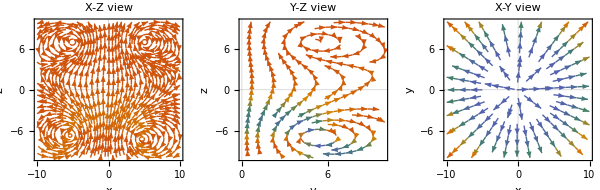

```mathematica
nX = 10.;
nY = 10.;
nZ = 10.;
yC = 0.0;
xC = 0.001;
zC = center1[[3]];
(*axiSymFieldPlotxz = StreamPlot[{axisymField[{x,yC,z},centers,radii,consts][[1]],axisymField[{x,yC,z},centers,radii,consts][[3]]},{x,-nX,nX},{z,-nZ,nZ},FrameLabel->{x,z},PlotLabel ->"X-Z view",StreamColorFunction->Automatic,StreamPoints -> Fine,LabelStyle->{15,GrayLevel[0]},PlotTheme -> "Scientific",ImageSize->400];*)
fieldPlotxz = StreamPlot[{b[{x,yC,z}][[1]],b[{x,yC,z}][[3]]},{x,-nX,nX},{z,-nZ,nZ},FrameLabel->{x,z},PlotLabel ->"X-Z view",StreamColorFunction->Automatic,StreamPoints -> Fine,LabelStyle->{15,GrayLevel[0]},PlotTheme -> "Scientific",ImageSize->400];
(*fieldPlotyz = StreamPlot[{b[{xC,y,z}][[2]],b[{xC,y,z}][[3]]},{y,0,nY},{z,-nZ,nZ},FrameLabel->{y,z},
PlotLabel ->"Y-Z view",StreamColorFunction->Automatic,StreamPoints -> Coarse,LabelStyle->{15,GrayLevel[0]},PlotTheme -> "Scientific",ImageSize->400];*)
fieldPlotxy = StreamPlot[{b[{x,y,zC}][[1]],b[{x,y,zC}][[2]]},{x,-nX,nX},{y,-nY,nY},FrameLabel->{x,y},
PlotLabel ->"X-Y view",StreamColorFunction->Automatic,StreamPoints -> Coarse,LabelStyle->{15,GrayLevel[0]},PlotTheme -> "Scientific",ImageSize->400];
GraphicsRow[{fieldPlotxz,fieldPlotxy},ImageSize->600]
```

## Computing the critical surfaces

```mathematica
xStart = -2;
xEnd = 2;
yStart = -2;
yEnd = 2;
zStart = -7;
zEnd = 7;
resX = 0.25;
resY = 0.25;
resZ = 0.25;
sigma3D = Table[{x,y,z,dfieldMagds[{x,y,z}]},{x,xStart,xEnd,resX},{y,yStart,yEnd,resY},{z,zStart,zEnd,resZ}];
```

```mathematica
xStart = -2;
xEnd = 2;
resX = 0.2;
yStart = -2;
yEnd = 2;
resY = resX;
z1 = center1[[3]];
sigmaSurface1 = Table[{zi = z/.With[{x=xi,y=yi},FindRoot[dfieldMagds[{xi,yi,z}] == 0,{{z,z1}}]],nonaxisymField[{xi,yi,zi},ϕ,θ][[1]],nonaxisymField[{xi,yi,zi},ϕ,θ][[2]],nonaxisymField[{xi,yi,zi},ϕ,θ][[3]]},{xi,xStart,xEnd,resX},{yi,yStart,yEnd,resY}];
```

```mathematica
zSigmaMinus = sigmaSurface1[[All,All,1]]//MatrixForm;
fieldXSigmaMinus = sigmaSurface1[[All,All,2]]//MatrixForm;
fieldYSigmaMinus = sigmaSurface1[[All,All,3]]//MatrixForm;
fieldZSigmaMinus = sigmaSurface1[[All,All,4]]//MatrixForm;
Export["zSigmaMinusCoil1.txt",zSigmaMinus,"Table"];
Export["fieldXSigmaMinusCoil1.txt",fieldXSigmaMinus,"Table"];
Export["fieldYSigmaMinusCoil1.txt",fieldYSigmaMinus ,"Table"];
Export["fieldZSigmaMinusCoil1.txt",fieldZSigmaMinus ,"Table"];
```

```mathematica
sigmaSurface1Plot = ListContourPlot[{sigmaSurface1[[All,All,1]]},DataRange->{{yStart,yEnd},{xStart,xEnd}},FrameLabel->{y,x},Mesh->None,InterpolationOrder->1,PlotLegends ->{Automatic},LabelStyle->{20,GrayLevel[0]},ImageSize->500]
hSigmaSurface1Plot =ListContourPlot[{Sqrt[sigmaSurface1[[All,All,2]]^2 + sigmaSurface1[[All,All,3]]^2+sigmaSurface1[[All,All,4]]^2]},DataRange->{{yStart,yEnd},{xStart,xEnd}},FrameLabel->{y,x},Mesh->None,InterpolationOrder->1,PlotLegends ->{Automatic},LabelStyle->{20,GrayLevel[0]},ImageSize->500]
```

```mathematica
xStart =-2;
xEnd =  2;
resX = 0.2;
yStart = -2;
yEnd = 2;
resY = resX;
Clear[X0,Y0,Z0]
tFinal = 200;
solSingleBounce= ParametricNDSolve[{X'[t] == vPar[t]b[X[t],Y[t],Z[t]][[1]],Y'[t] == vPar[t]b[X[t],Y[t],Z[t]][[2]],Z'[t] == vPar[t]b[X[t],Y[t],Z[t]][[3]],vPar'[t] == - dfieldMagds[X[t],Y[t],Z[t]],j'[t] == vPar[t]^2/Sqrt[2],X[0]==X0,Y[0]==Y0,Z[0] == Z0,vPar[0]==0.0,j[0] == 0,WhenEvent[vPar[t] == 0.0,If[Abs[t]> 0.1,"StopIntegration"]]},{X,Y,Z,vPar,j},{t,0,tFinal},{X0,Y0,Z0}];
solMultBounce= ParametricNDSolve[{X'[t] == vPar[t]b[X[t],Y[t],Z[t]][[1]],Y'[t] == vPar[t]b[X[t],Y[t],Z[t]][[2]],Z'[t] == vPar[t]b[X[t],Y[t],Z[t]][[3]],vPar'[t] == - dfieldMagds[X[t],Y[t],Z[t]],j'[t] == vPar[t]^2/Sqrt[2],X[0]==X0,Y[0]==Y0,Z[0] == Z0,vPar[0]==0.0,j[0] == 0,WhenEvent[vPar[t] == 0.0,Print[t,"\n",vPar[t],"\n",j[t]];{vPar[t]-> -vPar[t];t-> -t}]},{X,Y,Z,vPar,j},{t,0,tFinal},{X0,Y0,Z0}];
tEnd = First[vPar[xi,yi,zi]/.solSingleBounce][[1,-1]]
j[xi,yi,zi][tEnd]/.solSingleBounce
Plot[{vPar[xi,yi,zi][t]}/.solSingleBounce,{t,0,tEnd},PlotRange -> All]
Plot[{j[xi,yi,zi][t]}/.solSingleBounce,{t,0,tEnd},PlotRange -> All]
trajZX = ParametricPlot[{Z[xi,yi,zi][t],X[xi,yi,zi][t]}/.solSingleBounce,{t,0,tEnd},AxesLabel -> {z,x},LabelStyle->{15,GrayLevel[0]}, ImageSize->Large];
Show[fieldPlotxz,trajZX]
```

```mathematica
Export["SigmaSurface1_nonaxisym-caseIV.png",zSigmaSurface1Plot];
Export["hSigmaSurface1_nonaxisym-caseIV.png",hSigmaSurface1Plot];
Export["jSigmaSurface1_nonaxisym-caseIV.png",jSigmaSurface1Plot];

xi = -2.2;
yi = 0.0;
zi = 10^-5+z/.With[{x=xi,y=yi},FindRoot[dfieldMagds[x,y,z] == 0,{{z,z1}}]];
energy = Sqrt[fieldMagSqrd[xi,yi,zi]];
tFinal = 500;
j[x0_,y0_,z0_]:=Which[rhoSqrd1[x0,y0]==0,solSingleTraj= NDSolve[{X'[t] == vPar[t]bCenterCoil1[x1,y1,Z[t]][[1]],Y'[t] == vPar[t]bCenterCoil1[x1,y1,Z[t]][[2]],Z'[t] == vPar[t]bCenterCoil1[x1,y1,Z[t]][[3]],vPar'[t] == - dfieldMagds1[x1,y1,Z[t]],j'[t] == vPar[t]^2/Sqrt[2],X[0]==x0,Y[0]==y0,Z[0] == z0,vPar[0]==0.0,j[0] == 0,WhenEvent[vPar[t] == 0.0,If[Abs[t]> 0.1,"StopIntegration"]]},{X,Y,Z,vPar,j},{t,0,tFinal}];tEnd = First[vPar/.solSingleTraj][[1,-1]];First[j[tEnd[[2]]]/.solSingleTraj],
rhoSqrd2[x0,y0]==0,solSingleTraj= NDSolve[{X'[t] == vPar[t]bCenterCoil2[x2,y2,Z[t]][[1]],Y'[t] == vPar[t]bCenterCoil2[x2,y2,Z[t]][[2]],Z'[t] == vPar[t]bCenterCoil2[x2,y2,Z[t]][[3]],vPar'[t] == - dfieldMagds2[x2,y2,Z[t]],j'[t] == vPar[t]^2/Sqrt[2],X[0]==x0,Y[0]==y0,Z[0] == z0,vPar[0]==0.0,j[0] == 0,WhenEvent[vPar[t] == 0.0,If[Abs[t]> 0.1,"StopIntegration"]]},{X,Y,Z,vPar,j},{t,0,tFinal}];tEnd = First[vPar/.solSingleTraj][[1,-1]];First[j[tEnd[[2]]]/.solSingleTraj],
True,solSingleTraj= NDSolve[{X'[t] == vPar[t]bGen[X[t],Y[t],Z[t]][[1]],Y'[t] == vPar[t]bGen[X[t],Y[t],Z[t]][[2]],Z'[t] == vPar[t]bGen[X[t],Y[t],Z[t]][[3]],vPar'[t] == - dfieldMagdsGen[X[t],Y[t],Z[t]],j'[t] == vPar[t]^2/Sqrt[2],X[0]==x0,Y[0]==y0,Z[0] == z0,vPar[0]==0.0,j[0] == 0,WhenEvent[vPar[t] == 0.0,If[Abs[t]> 0.1,"StopIntegration"]]},{X,Y,Z,vPar,j},{t,0,tFinal}];tEnd = First[vPar/.solSingleTraj][[1,-1]];First[j[tEnd[[2]]]/.solSingleTraj]];
zhjSigmaMinusCoil1=Table[{zi = 10^-5 + z/.With[{x=xi,y=yi},FindRoot[dfieldMagds[x,y,z] == 0,{{z,z1}}]],Sqrt[fieldMagSqrd[xi,yi,zi]],j[xi,yi,zi]},{xi,-2,2,0.2},{yi,-2,2,0.2}];
```

```mathematica
zSigmaMinus = zhjSigmaMinusCoil1[[All,All,1]]//MatrixForm;
hSigmaMinus = zhjSigmaMinusCoil1[[All,All,2]]//MatrixForm;
jSigmaMinus = zhjSigmaMinusCoil1[[All,All,3]]//MatrixForm;
Export["zSigmaMinusCoil1.txt",zSigmaMinus,"Table"];
Export["hSigmaMinusCoil1.txt",hSigmaMinus,"Table"];
Export["jSigmaMinusCoil1.txt",jSigmaMinus,"Table"];
```